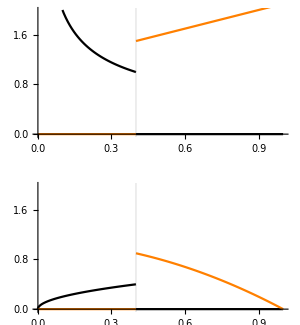

/Users/johnbunce/Dropbox/Matsigenka-Mestizo_project_2014/perception_analysis/xcult_dynamics/figures/affplots.pdf

```mathematica
(*equilib between in-group affinity and inter-group coord payoff*)
ClearAll["Global`*"];

bStar=0.5;
aStar=0.4;

affpayplot=Show[
Plot[(aStar/x)^0.5,{x,0,0.4},PlotRange->{{0,1},{-0.01,2}},AspectRatio->0.5,PlotStyle->Black,PlotStyle->Black,GridLines->{{{0.4,{CapForm["Butt"],Dashing[0.03],Black}}},{}}],
Plot[0,{x,0.4,1},PlotStyle->Black],
Plot[1+bStar+(x-aStar),{x,0.4,1},PlotStyle->Orange],
(*Plot[1+bStar+(x-aStar),{x,0.4,1},PlotStyle->Orange],*)
Plot[0,{x,0,0.4},PlotStyle->Orange]
];

affutilplot=Show[
Plot[x*(aStar/x)^0.5,{x,0,0.4},PlotRange->{{0,1},{-0.01,2}},AspectRatio->0.5,PlotStyle->Black,PlotStyle->Black,GridLines->{{{0.4,{CapForm["Butt"],Dashing[0.03],Black}}},{}}],
Plot[0,{x,0.4,1},PlotStyle->Black],
Plot[(1+bStar+(x-aStar))*(1-x),{x,0.4,1},PlotStyle->Orange],
Plot[0,{x,0,0.4},PlotStyle->Orange]
];


affplots=GraphicsGrid[
{{affpayplot},{affutilplot}},

Spacings->{
{
Scaled[0.5], (*horizontal spacing: before, middle, end of row of figures*)
Scaled[0.5]
},
{
Scaled[0.5], (*vertical spacing: above, middles, bottom of column of figures*)
Scaled[0.25],
Scaled[0.5]
}
},

Frame->True,
FrameStyle->Directive[White],

xmv=150;
ymv=-25;

xmv2=150;
ymv2=-200;

Epilog->{
Inset[Style[a,12, Italic,FontFamily->"Cambria"],{410,-185}],
Inset[Style[a,12, Italic,FontFamily->"Cambria"],{410,-395}],
Inset[Style[Superscript[a,"*"],12, Italic,FontFamily->"Cambria"],{205,-20}],
Inset[Style[Rotate["Payoff Valuation",90 Degree],12,FontFamily->"Cambria"],{30,-110}],
Inset[Style[Rotate["Utility",90 Degree],12,FontFamily->"Cambria"],{30,-320}],

Inset[Style[HoldForm[Superscript[b,"*"]],12,FontFamily->"Cambria"],{70+xmv,-68+ymv},Left],
Inset[Style["}",25,FontFamily->"Cambria"],{55+xmv,-68+ymv},Left],
Inset[Style[HoldForm[TraditionalForm[Subscript["val",i]=(Superscript[a,-1]*Superscript[a,"*"])^(1/2)]],12,FontFamily->"Cambria"],{120+xmv,-85+ymv},Left],
Clear[b];
Inset[Style[HoldForm[Subscript["val",o]=1+Superscript[b,"*"]+a-Superscript[a,"*"]],12,FontFamily->"Cambria"],{120+xmv,-130+ymv},Left],
{AbsoluteThickness[2],Black,Line[{{80+xmv,-90+ymv},{110+xmv,-90+ymv}}]},
{AbsoluteThickness[2],Orange,Line[{{80+xmv,-130+ymv},{110+xmv,-130+ymv}}]},


Inset[Style[HoldForm[Subscript["util",i]=a*Subscript["val",i]],12,FontFamily->"Cambria"],{120+xmv2,-60+ymv2}, Left],
Clear[b];
Inset[Style[HoldForm[Subscript["util",o]=(1-a)*Subscript["val",o]],12,FontFamily->"Cambria"],{120+xmv2,-100+ymv2},Left],
{AbsoluteThickness[2],Black,Line[{{80+xmv2,-60+ymv2},{110+xmv2,-60+ymv2}}]},
{AbsoluteThickness[2],Orange,Line[{{80+xmv2,-100+ymv2},{110+xmv2,-100+ymv2}}]}


},
ImageSize->300
](*Graphics Grid*)

(*
Export["C:\\Users\\jabunce\\Dropbox\\Matsigenka-Mestizo_project_2014\\perception_analysis\\xcult_dynamics\\figures\\affplots.pdf",affplots,"PDF"]
*)
Export["/Users/johnbunce/Dropbox/Matsigenka-Mestizo_project_2014/perception_analysis/xcult_dynamics/figures/affplots.pdf",affplots,"PDF"]
```